```mathematica
(* Classical Mechanics in Wolfram Language *)
```

```mathematica
(* Kinematics: Projectile motion in 3D with gravity *)
r[t_]:={10t,5 t,20 t-(1/2) 9.8 t^2};
v[t_]:=D[rproj[t],t];
a[t_]:=D[rproj[t],{t,2}];

(* Function *)
r[t]
v[t]
a[t]

(* Trajectory *)
ParametricPlot3D[r[t],{t,0,4},AxesLabel->{"x","y","z"},PlotStyle->Thick]
```

{10 t,5 t,20 t-4.9 t^2}

{10,5,20-9.8 t}

{0,0,-9.8}

-Graphics3D-

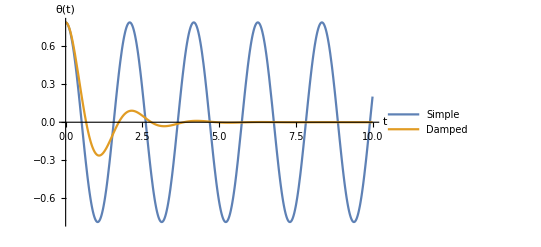

```mathematica
(* Newtonian Mechanics: Pendulum *)
l=1;g=9.8;
theta0=Pi/4;omega0=0;
b=2; (*damping coefficient*)

(* Pendulum without damping *)
solSimple=NDSolve[{theta''[t]+(g/l) Sin[theta[t]]==0,theta[0]==theta0,theta'[0]==omega0},theta,{t,0,10}];

(* Damped Pendulum *)
solDamped=NDSolve[{theta''[t]+b theta'[t]+(g/l) Sin[theta[t]]==0,theta[0]==theta0,theta'[0]==omega0},theta,{t,0,10}];

(* Plot *)
Plot[Evaluate[{theta[t]/. solSimple,theta[t]/. solDamped}],{t,0,10},PlotLegends->{"Simple","Damped"},AxesLabel->{"t","θ(t)"}]

(*Animation*)
Animate[Graphics[{Line[{{0,0},l {Sin[theta[t]/. solDamped[[1]]],-Cos[theta[t]/. solDamped[[1]]]}}],Disk[l {Sin[theta[t]/. solDamped[[1]]],-Cos[theta[t]/. solDamped[[1]]]},0.02]},PlotRange->{{-l,l},{-2 l,0}},Axes->True],{t,0,10}]
```